# Post-processing for Termens_et_al_2025_Cell_Clusters

## Figures and gifs for a semicircular epithelial cluster

Main FreeFem++ script for the demo simulations associated with:

Termens et al. (2025) Cell clusters sense their global shape to drive collective migration

This notebook:
 - defines the physical and numerical parameters
 - runs a representative simulation
 - writes output files to disk for post-processing

 Author: Joan Térmens
Last update: 26 Jan 2026

Input:
-  ./semicircle_test/ from solver_pv.edp or
- ./semicircle_test.tar.xz

Output:
- Results are written to the directory specified by `rootDir/simulName`.

## Notebook Setup

### Folder configuration

```mathematica
ClearAll;

SetDirectory[NotebookDirectory[]]; (*Set the notebook's directory as the current working directory, will depend on your folder structure*)

simulName="semicircle_test";

(*Folder management*)
pathSimul = "";

If[DirectoryQ[simulName],(*Check if the simulation folder exists*)
pathSimul=simulName,
If[FileExistsQ[simulName<>".tar.gz"],(*Check if a compressed simulation folder exists*)
pathSimul=ExtractArchive[simulName<>".tar.gz",$TemporaryDirectory,OverwriteTarget -> True];
pathSimul=StringRiffle[Most@StringSplit[pathSimul[[1]],"/"],{"/","/",""}],
Print[StringForm["Input folder ``/ or `` not found.",simulName,simulName<>".tar.xz"]];Interrupt[];
]
];

pathMeshes=FileNameJoin[{pathSimul,"msh"}]; (*Folder storing the meshes*)
pathSolutions=FileNameJoin[{pathSimul,"local_sol"}]; (*Folder storing the solutions*)
pathResults =simulName<>"_plots";(*Folder where we will export the resulting plots*)

(*Create the pathResults folder if it does not already exists*)
If[!DirectoryQ[pathResults],CreateDirectory[pathResults]];
```

### Custom read of .txt and .msh files

```mathematica
(*The functions defined here to read files are designed to be roboust and properly work regardless of the compression or owner of the simulation results;- We use Import[] OVER OpenRead[] as the second one does not work with files owened by root (such as the ones generated in a devcontainer);
- We parse the lines with ReadList[] over ToExpression[] as the latter sometimes has given us problems with machine size numbers;  
*)

(*Parser of a string line with number separated by whitespace*)
readLine[line_]:=Module[{strm,lineData},
strm=StringToStream[line];
lineData=First[ReadList[strm,Number,RecordLists->True]];
Close[strm];
lineData
]

(*Custom read of a txt file, skips the headers (first nheader lines) and reads everything else as numbers, while converting lines into lists*)
ReadFile[filename_,nheader_:0]:=Module[{lines,data},
lines=Import[filename,"Lines"];
lines=Drop[lines,nheader];(*Drop the header lines*)
data=Map[readLine,lines];
data
]
(*Custom read of an .msh file. Colud save the mesh labels and returns nV (num. vertices), nT (num.triangles), nbE (num. boundary edges), together with lists of the vertices, triangles and boundary edges.*)
ReadMshFile[filename_,saveLabels_:False]:=Module[{data,nV,nT,nbE,iniIndex,lastCol,meshVertices,meshTriangles,bmeshEdges},
data=ReadFile[filename,0]; (*read the msh file using our custom ReadFile function*)

(*initial index of the lines to parse*)
iniIndex=1;
(*if saveLabels=False, lastCol=-2 avoids saving the labels. Else, lastCol=-1 and labels are saved*)
lastCol=If[saveLabels,-1,-2];
(*nV = num. vertices, nT = num. triangles, nbE = num. boundary edges*)
{nV,nT,nbE}=data[[iniIndex]];
(*Parse the vertices' positions*)
iniIndex+=1;
meshVertices=data[[iniIndex;;nV+(iniIndex-1),;;lastCol]]; (*selects from 2 (staring index) of the vertices to (2-1)+nV which is the index of the last vertex)*)
(*Parse the mesh triangles*)
iniIndex+=nV;
meshTriangles=data[[iniIndex;;nT+(iniIndex-1),;;lastCol]];
(*Parse the boundary edges*)
iniIndex+=nT;
(*Take into account that in adaptative meshes the internal boundary is also saved, so we need to
filter it using its label*)
bmeshEdges=Select[data[[iniIndex;;]],#[[-1]]==1&][[All,;;lastCol]];
nbE = Length[bmeshEdges];
{nV,nT,nbE,meshVertices,meshTriangles,bmeshEdges} (*Return everything*)
]
```

### Functions for FEM load and process

```mathematica
<<NDSolve`FEM` (*Package to interpolate Finite Element solutions*)

(*Load the parameters of simulations from their params.csv files;
- simulName: name of the simulation to load;
- gsplit: we will load 1 frame every gsplit ones, so gsplit = 3 means we will load 1st, 3rd, 6th, etc. timesteps;
- extremeFramesOnly: if True will only load the 1st and last frames of the evolution;
- limitFrames: if set to an integer, will load frames unit reaching it;
*)
loadParams[simulName_,gsplit_:1,extremeFramesOnly_:False,limitFrames_:None]:=Module[
{params,paramsDict,paramNames,paramVals,nFrames},(*Those are the variables defined inside the function (Module)*)

(params=Import[FileNames["params.csv",pathSimul][[1]],"CSV"]);
paramNames=params[[1]];(*Extract the params names*)
(*params[[2]] would return strings identifying the units of each parameter*)
paramVals=params[[3]];(*Extract the params values*)
paramsDict=AssociationThread[paramNames,ToExpression[paramVals]];(*Create an association from the imported params*)
(*Associations are hashable lists of key -> value, represent the same data structure tha dictionaries in python or hash maps in C++*)

(*Compute other useful parameters*)
If[extremeFramesOnly,nFrames=2,nFrames=Ceiling[Length[FileNames["mesh*",pathMeshes]]]/gsplit];

(*Add the new parameters*)
AssociateTo[paramsDict,{
"dtOut"->paramsDict[["dt"]]*paramsDict[["dsave"]]*gsplit,
"nFrames"->nFrames,
"limitFrame"->If[NumericQ[limitFrames],Min[limitFrames,nFrames],nFrames]
}];

{<|simulName->#|>,Keys[#]}&[paramsDict](*Return the parameters dictionary plus its list of keys*)]
(*---------------------------------------------------------------------------------------------------------------------------------*)

(*Load the time and variables integrated during the simulation's run;
- simulName: name of the simulation to load;
- gsplit: we will load 1 frame every gsplit ones, so gsplit = 3 means we will load 1st, 3rd, 6th, etc. timesteps;
- extremeFramesOnly: if True will only load the 1st and last frames of the evolution;
- onlyY: if True will only load the Y component of each of the computed vectors
*)
loadGlobalSols[simulName_,gsplit_:1,extremeFramesOnly_:False,onlyY_:False]:=Module[
{globalSols,globalSolDict,globalSolNames,globalSolVals,frames,rC,tC,vC},
If[extremeFramesOnly,frames={3,-1},frames=3;;All;;gsplit]; (*Frames to extract*)

(globalSols=Import[FileNames["global_sol.csv",pathSimul][[1]]]);

globalSolNames=globalSols[[1]];(*Extract the names of the global solutions*)
globalSolVals=Transpose[globalSols[[frames]]]; (*Extract the values of the global solutions and transpose the lines*)
globalSolDict=AssociationThread[globalSolNames,ToExpression[globalSolVals]]; (*Create an association from the imported global sols*)

If[onlyY,(*Only return the values for the Y-coord*)
KeyDropFrom[globalSolDict,{"Xcm","Txcm","Vxcm","Vxavg","Axcm", "Ix","divXcm", "divXavgcm", "divTermsX"}]
];

{<|simulName->#|>,Keys[#]}&[globalSolDict](*Return the globalSols dictionary plus its list of keys*)]
(*---------------------------------------------------------------------------------------------------------------------------------*)

(*Load the solutions of the local fields which depend on {x,y,t};
- simulName: name of the simulation to load;
- gsplit: we will load 1 frame every gsplit ones, so gsplit = 3 means we will load 1st, 3rd, 6th, etc. timesteps;
- extremeFramesOnly: if True will only load the 1st and last frames of the evolution;
- onlyY: if True will only load the Y component of each of the computed vectors;
- params: we need to pass the parameters as an argument as we need R0 to des-adimensionalize the mesh, or to compute the local traction;
(All the other fiels are des-adimensionalized by default by the simulation algorithm.)
*)
loadLocalSols[simulName_,gsplit_:1,extremeFramesOnly_:False,params_:False]:=Module[
{fileSols,fileMeshes,localSols,localSolsToLoad,localSolsInt,meshData,rC},

(*Find the local solutions& mesh files*)
fileSols=FileNames["sol*",pathSolutions];(*Solutions in .txt format, colud be improved with a native format*)
fileMeshes=FileNames["mesh*",pathMeshes];(*Meshes in .msh format*)

If[extremeFramesOnly&&gsplit==1,
fileSols=fileSols[[{1,-1}]];
fileMeshes=fileMeshes[[{1,-1}]];
];

(*Load the meshes*)meshData=AssociationThread[{"nV","nT","nbE","meshVertices","meshTriangles","bmeshEdges"},Transpose[ParallelMap[ReadMshFile[#]&,fileMeshes[[;;;;gsplit]]]]];

(*Load the simulation's solutions*)
localSols=ParallelMap[ReadFile[#,4]&,fileSols[[;;;;gsplit]]];
(*If gsplit remains constant,Length[Sols],Length[meshVertices],...,Lenght[globalSolSimul] should be equal*)

(*Assigns the number of the column to its name*)
(*Comment the ones that won't be loaded*)
localSolsToLoad=<|
"px"->1,(*x-component of the polarity, [adim]*)
"py"->2,(*y-component of the polarity, [adim]*)
"vx"->3,(*x-component of the velocity, [μm/s]*) 
"vy"->4(*,*) (*y-component of the velocity, [μm/s]*) 
(*"dpxx"->5,*) (*x-component of the gradient of px, [1/μm]*)
(*"dpxy"->6,*) (*y-component of the gradient of px, [1/μm]*) 
(*"dpyx"->7,*) (*x-component of the gradient of py, [1/μm]*)
(*"dpyy"->8,*) (*y-component of the gradient of py, [1/μm]*)
(*"dvxx"->9,*) (*x-component of the gradient of vx, [1/s]*)
(*"dvxy"->10,*) (*y-component of the gradient of vx, [1/s]*)
(*"dvyx"->11,*) (*x-component of the gradient of vy, [1/s]*)
(*"dvyy"->12,*) (*y-component of the gradient of vy, [1/s]*)
(*"dpxxx"->13,*) (*xx-component of the hessian of px, [1/μm.b2]*)
(*"dpxxy"->14,*) (*xy-component of the hessian of px, [1/μm.b2]*)
(*"dpxyx"->15,*) (*yx-component of the hessian of px, [1/μm.b2]*)
(*"dpxyy"->16,*) (*yy-component of the hessian of px, [1/μm.b2]*)
(*"dpyxx"->17,*) (*xx-component of the hessian of py, [1/μm.b2]*)
(*"dpyxy"->18,*) (*xy-component of the hessian of py, [1/μm.b2]*)
(*"dpyyx"->19,*) (*yx-component of the hessian of py, [1/μm.b2]*)
(*"dpyyy"->20*) (*yy-component of the hessian of py, [1/μm.b2]*)
|>;

(*Process the meshes and solutions*)
localSolsInt=ParallelMap[(*Interpolate the solutions in parallel*)
processDat[simulName,#[[1]],#[[2]],localSolsToLoad,params]&,(*Function that interpolates the solutions*)
Table[{localSols[[n]],meshData[[All,n]]},{n,1,Length[localSols]}](*Iterate through the meshes and solutions*)
];

{<|simulName->#|>,Keys[#]}&[Merge[localSolsInt,Identity]] (*Fastest& cleanest way to do it*)]

(*---------------------------------------------------------------------------------------------------------------------------------*)

(*Interpolate the solutions using the mesh data*)
processDat[simulName_,sols_,meshData_,localSolsToLoad_,params_]:=Module[
{mesh,localSolsInt,SortedBC,xMin,xMax,yMin,yMax},

{xMin,xMax}=MinMax[1.05*params[["lengthScale"]]*meshData[["meshVertices",All, 1]]];
{yMin,yMax}=MinMax[1.05*params[["lengthScale"]]*meshData[["meshVertices",All, 2]]];

(*Generate the mesh*)mesh=ToElementMesh["Coordinates"->params["lengthScale"]*meshData[["meshVertices",All, ;;2]],"MeshElements"->{TriangleElement[meshData[["meshTriangles",All, ;;3]]]}];
(*Parting,[[]],both the vertices and triangles avoids to process the labels,if loaded*)

(*Print["Num. coordinates = ",Length[mesh["Coordinates"]],", Num. data points = ",Length[sols[[All,localSolsToLoad[[1]]]]]];*)
(*bmesh=ToBoundaryMesh[mesh];*)(*Not needed, but colud be useful*)

localSolsInt=<|"mesh"->mesh|>;(*Add to the solution*)

(*Interpolate the imported data*)
AssociateTo[localSolsInt,KeyValueMap[#1->ElementMeshInterpolation[{mesh},sols[[All,#2]],InterpolationOrder->1]&,localSolsToLoad]]; (*The interpolation is computationallly expensive, so it's good to minimize the num. of variables*)

(*Interpolate other fields*)
AssociateTo[localSolsInt,{
(*"absV"->ElementMeshInterpolation[{mesh},solsDict[["vx",2]]*Sqrt[Power[sols[[All,solsDict[["vx",1]]]],2]+Power[sols[[All,solsDict[["vy",1]]]],2]],InterpolationOrder->1],*)
(*"divV"->ElementMeshInterpolation[{mesh},solsDict[["dvxx",2]]*(sols[[All,solsDict[["dvxx",1]]]]+sols[[All,solsDict[["dvyy",1]]]]),InterpolationOrder->1],*)
(*"rotV"->ElementMeshInterpolation[{mesh},solsDict[["dvyx",2]]*(sols[[All,solsDict[["dvyx",1]]]]-sols[[All,solsDict[["dvxy",1]]]]),InterpolationOrder->1],*)
"sortedBC"->Normal[params[["lengthScale"]]]*meshData[["meshVertices"]][[meshData[["bmeshEdges",All,1]], ;;2]],
"xMin"->xMin,"xMax"->xMax,"yMin"->yMin,"yMax"->yMax
}];
localSolsInt]
```

### Configuration of the Visualization

```mathematica
(*ResourceFunction["AddMatplotlibColors"] [];*)(*Adds the mpl colormaps by Nathaniel Smith and Stefan van der Walt used by Matplotlib*)
```

```mathematica
fontStyle={FontFamily->"Helvetica [adobe]",FontSize->12,Black};
fontStyleSmall=fontStyle/.{12->10};
fontStyleGray=fontStyle/.{Black->Gray};

pSize=.01;
lineStyle=Directive[Black,Thickness->.002];
dashedLineStyle=Directive[Gray,AbsoluteThickness[.002],Dashed];
arrowStyle=Directive[Gray,Thickness->.002,Arrowheads[.025]];

paletteName="RedBlueTones";
palette=ColorData[paletteName];

(*Some nice well-contrasting colors*)
contrastBlue=RGBColor["#5e81b5"];
contrastRed=RGBColor["#eb6235"];
contrastOrange=RGBColor["#e19c24"];
lightOrange=RGBColor["#eab965"];
contrastPurple=RGBColor["#8677b3"];
lightPurple=RGBColor["#c9a0dc"];

contrastGreen=ColorData[97][15];
contrastYellow=ColorData[97][8];

(*Scales based on the above colors*)
blueScale={nColors}|->Map[Blend[{RGBColor["#9ecae1"],contrastBlue,RGBColor["#08519c"]},#]&,Subdivide[nColors-1]];
orangeScale={nColors}|->Map[Blend[{RGBColor["#fdae6b"],contrastOrange,RGBColor["#a63603"]},#]&,Subdivide[nColors-1]];
redScale={nColors}|->Map[Blend[{RGBColor["#fc9272"],contrastRed,RGBColor["#a50f15"]},#]&,Subdivide[nColors-1]];
purpleScale={nColors}|->Map[Blend[{RGBColor["#bcbddc"],contrastPurple,RGBColor["#54278f"]},#]&,Subdivide[nColors-1]];

colSize=500; (*good size for 1-column figure in a double column paper*)
```

## Plots and analysis

### Load the simulations

```mathematica
gsplit=5;
extremeFramesOnly=False;
onlyY=False;

If[extremeFramesOnly,gsplit=1];
```

#### Load the parameters

```mathematica
(*Load the parameters of the simulations*)
(*!! Different simulations could have different parameters, like the addition of surface tension or a domain defined by other parameters rather than {R0,cut}. To fix that, It may be necessary to manage datasets with missing data.*)
{params,paramsKeys}=loadParams[simulName,gsplit,extremeFramesOnly];(*Create params Dataset*)

Print["Parameters Keys: ",paramsKeys];
Dataset[params](*Dataset helps for visualitzation, but, for me, it's unpractical for managing the solutions*)
```

Parameters Keys: {domain,cut,R0,lengthScale,fracRarc,obd,ibd,Lc,lambda,La,eta,xi,zi,zeta,tscale,dt,dsave,dtOut,nFrames,limitFrame}

To ease the manipulation of the physical parameters I usually define some functions that depend on the simulation

```mathematica
cut[simulName_:simulName]:=params[[simulName,"cut"]];
R0[simulName_:simulName]:=params[[simulName,"R0"]]; (*If all the simulations share a parameter value, you can default it and call it like R0[]*)
lenghtScale[simulName_:simulName]:=params[[simulName,"lenghtScale"]];
λ[simulName_:simulName]:=params[[simulName,"lambda"]];
La[simulName_:simulName]:=params[[simulName,"La"]];
η[simulName_:simulName]:=params[[simulName,"eta"]];
ξ[simulName_:simulName]:=params[[simulName,"xi"]];
ζi[simulName_:simulName]:=params[[simulName,"zi"]];
ζ[simulName_:simulName]:=params[[simulName,"zeta"]];

lastFrame[simulName_:simulName]:=params[[simulName,"limitFrame"]];
```

#### Load the global solutions (Integrated variables)

```mathematica
(*Load evolution of integrated magnitudes*)
{globalSols,globalSolsKeys}=loadGlobalSols[simulName,gsplit,extremeFramesOnly,onlyY];

Print["Local Solutions Keys: ",globalSolsKeys];
Print["  -  Dimensions of localSols for " ,#,": ",Join[Dimensions[globalSols[[#]]],Dimensions[globalSols[[#,1]]]]]&[simulName];
```

Local Solutions Keys: {Time,Area,Xcm,Ycm,avgDivV,Vxcm,Vycm,Vxavg,Vyavg,Axcm,Aycm,Txavg,Tyavg,divXcm,divYcm,divXavgcm,divYavgcm,divTermsX,divTermsY,MxxT,MxyT,MyyT,MxxF,MxyF,MyyF,MxxxT,MxxyT,MxyxT,MxyyT,MyyxT,MyyyT,MxxxF,MxxyF,MxyxF,MxyyF,MyyxF,MyyyF,Ix,Iy}

-  Dimensions of localSols for semicircle_test: {39,20}

#### Load the local solutions

```mathematica
(*Load evolution of fields*)
{localSols,localSolsKeys}=loadLocalSols[#,gsplit,extremeFramesOnly,params[[#]]]&[simulName];

Print["Local Solutions Keys: ",localSolsKeys];
Print["  -  Dimensions of localSols for " ,#,": ",Join[Dimensions[localSols[[#]]],Dimensions[localSols[[#,1]]]]]&[simulName];
```

Local Solutions Keys: {mesh,px,py,vx,vy,sortedBC,xMin,xMax,yMin,yMax}

-  Dimensions of localSols for semicircle_test: {10,20}

### Render the plots and gifs

#### Plots of the global variables (V_CM, Area, etc.)

```mathematica
(*At this point we have arrays of both time (in s) and velocities (in μm/s), positions, etc. We want to combine both and to change the units to μm/h*)
ΔYcm[simulName_]:=Transpose[{
(1/3600) globalSols[simulName,"Time"], (*x-coordinate, change units to h*)
globalSols[simulName,"Ycm"] -globalSols[simulName,"Ycm"][[1]](*y-coordinate*)
}];

relativeArea[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],globalSols[simulName,"Area"]/globalSols[simulName,"Area"][[1]] }];
Ix[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],globalSols[simulName,"Ix"] /10000}];(*Divide by 10^5 to avoid large numbers in the y-axis*)
Iy[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],globalSols[simulName,"Iy"] /10000}];

(*Change units to h and divide by friction, so 1/ξ∫Subscript[ζ, i](y)Subscript[p, y] ⅆS*)
TractionIntegralY[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],(3600/ξ[simulName]) globalSols[simulName,"Tyavg"]}];

SpreadIntegralY[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],(3600) globalSols[simulName,"divTermsY"] }];

VcmY[simulName_]:=Transpose[{(1/3600) globalSols[simulName,"Time"],(3600/ξ[simulName]) globalSols[simulName,"Tyavg"]+(3600) globalSols[simulName,"divTermsY"]}];
(*
Here we compute the Vcm from the formula, Subscript[V, CM] = 1/A(1/ξ∫Subscript[ζ, i](y)Subscript[p, y] ⅆS+∫(y-Subscript[Y, CM])∇·vⅆS);
but there are other options;
- Vycm is the Vcm computed with a numeric derivative, Subscript[V, CM,y]^n=(Subscript[Y, CM]^n-Subscript[Y, CM]^(n-1))/(t^n-t^(n-1));
- Vyavg is 1/A∫Subscript[v, y] ⅆS and could be used instead of the traction integral, as force balance implies ξ∫Subscript[v, y] ⅆS = ∫Subscript[ζ, i] Subscript[p, y] ⅆS;
If the results do not make sense it could be convenient to check that the force balance is satisfyed.
*)
```

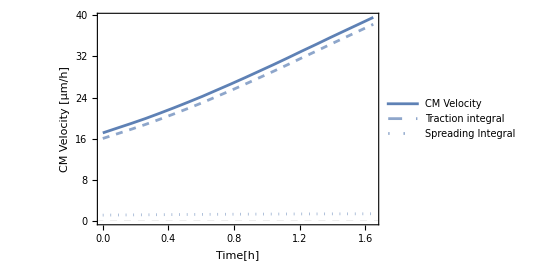

```mathematica
(*Start by comparing the evolution of the CM Velocity, as well as its components, for both clusters*)
plotVcmDecomp[padding_,size_]:=ListLinePlot[{
VcmY[simulName],(*Solid lines*)
TractionIntegralY[simulName],(*Dashed lines*)
SpreadIntegralY[simulName](*Dotted lines*)
},
PlotStyle->Flatten[Table[
{Directive[{colour}],Directive[{colour,Dashed,Opacity[.7]}],Directive[{colour,Dotted,Opacity[.7]}]},
{colour,{contrastBlue,contrastRed}}]],
PlotLegends->Placed[
{"CM Velocity","Traction integral","Spreading Integral"},
{.7,.3}],
PlotRange->Automatic,
GridLines->{None,{0}},
GridLinesStyle->dashedLineStyle,
LabelStyle->fontStyle,
Axes->False,
AspectRatio->2/3,
ImagePadding->padding,(*How much space is left around the plot*)
Frame->True,
FrameLabel->{"Time[h]","CM Velocity [μm/h]"},
ImageSize->size
];

padding={{50,5},{50,5}};
size= 2colSize/3;

plotVcmDecomp[padding,size]
```

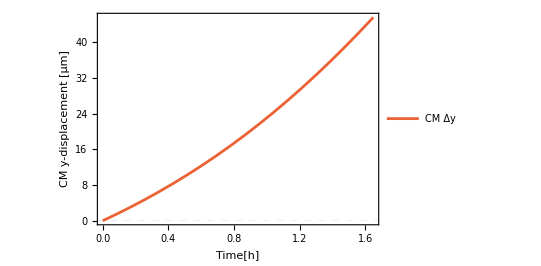
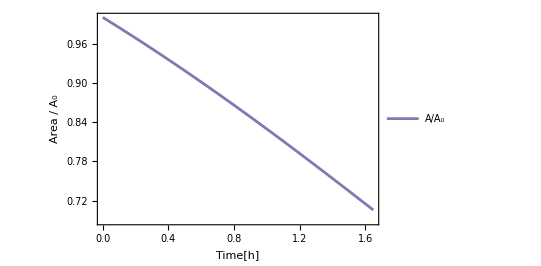
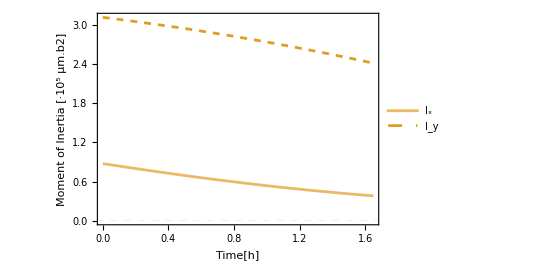

```mathematica
(*Plots of geometric integrals: Area, Ycm & inertia moments*)
plotYcm[padding_,size_]:=ListLinePlot[
ΔYcm[simulName],
PlotStyle->contrastRed,
PlotLegends->Placed[
{"CM Δy"},
{.2,.8}],
PlotRange->Automatic,
GridLines->{None,{0}},
GridLinesStyle->dashedLineStyle,
LabelStyle->fontStyle,
Axes->False,
AspectRatio->2/3,
ImagePadding->padding,(*How much space is left around the plot*)
Frame->True,
FrameLabel->{"Time[h]","CM y-displacement [μm]"},
ImageSize->size
];

plotArea[padding_,size_]:=ListLinePlot[
relativeArea[simulName],
PlotStyle->contrastPurple,
PlotLegends->Placed[
{"A/A_0"},
{.8,.8}],
PlotRange->Automatic,
GridLines->{None,{0}},
GridLinesStyle->dashedLineStyle,
LabelStyle->fontStyle,
Axes->False,
AspectRatio->2/3,
ImagePadding->padding,(*How much space is left around the plot*)
Frame->True,
FrameLabel->{"Time[h]","Area / A_0"},
ImageSize->size
];

plotInertia[padding_,size_]:=ListLinePlot[{
Ix[simulName],(*Solid lines*)
Iy[simulName](*Dashed lines*)
},
PlotStyle->Flatten[Table[
{Directive[{colour,Opacity[.7]}],Directive[{colour,Dashed}]},
{colour,{contrastOrange}}]],
PlotLegends->Placed[
{"I_x","I_y"},
{.25,.7}],
PlotRange->Automatic,
GridLines->{None,{0}},
GridLinesStyle->dashedLineStyle,
LabelStyle->fontStyle,
Axes->False,
AspectRatio->2/3,
ImagePadding->padding,(*How much space is left around the plot*)
Frame->True,
FrameLabel->{"Time[h]","Moment of Inertia [·10⁵ μm.b2]"},
ImageSize->size
];

size= 2 colSize/3;
{plotYcm[padding,size],plotArea[padding,size],plotInertia[padding,size]}
```

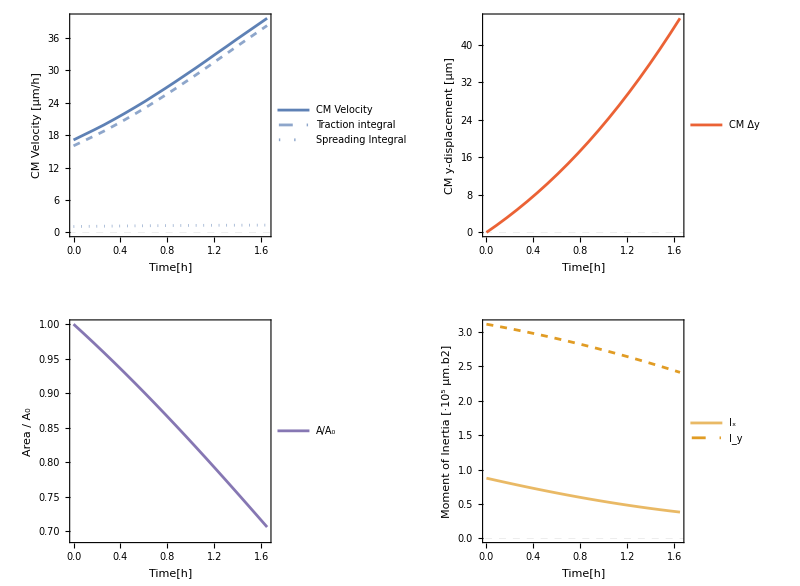

```mathematica
figPlotIntegrals=Show[GraphicsGrid[
{
{plotVcmDecomp[padding,size],plotYcm[padding,size]},
{plotArea[padding,size],plotInertia[padding,size]}
},
ImageSize->4colSize/3
],
PlotLabel->"Evolution of some integrated variables for "<>simulName
]
```

```mathematica
Export[FileNameJoin[{pathResults,"global_variables.png"}],figPlotIntegrals,"PNG"](*You could use other formats, like PDF or SVG, but PNG is the most straighforward.*)
```

semicircle_test_plots/global_variables.png

#### Static plots of the local variables (velocity and traction)

```mathematica
Ycm0[simulName_]:=globalSols[simulName,"Ycm"][[1]];

plotFrame[simulName_,frame_,field_,range_,padding_,plotSize_]:=Module[
{mesh,mr,plotFieldBack,plotFieldFront,plotBack,plotFront,label,xmin,xmax,ymin,ymax},
mesh=localSols[simulName,"mesh"][[frame]];
mr=MeshRegion[mesh];

xmin=localSols[simulName,"xMin"][[frame]];
xmax=localSols[simulName,"xMax"][[frame]];
ymin=localSols[simulName,"yMin"][[frame]];
ymax=localSols[simulName,"yMax"][[frame]];

Which[
field=="y-vel",
plotFieldBack=3600 (localSols[simulName,"vy"][[frame]])[x,y]; label="y-Velocity [μm/h]";
plotFieldFront={(localSols[simulName,"vx"][[frame]])[x,y],(localSols[simulName,"vy"][[frame]])[x,y]},
field=="y-trac",
plotFieldBack=ζi[] (localSols[simulName,"py"][[frame]])[x,y]; label="y-Traction [kPa/μm]";
plotFieldFront={ζi[](localSols[simulName,"px"][[frame]])[x,y],ζi[](localSols[simulName,"py"][[frame]])[x,y]}
];


plotBack=DensityPlot[plotFieldBack,
{x,xmin,xmax},{y,ymin,ymax},
RegionFunction->Function[{x,y},RegionMember[mr,{x,y}]],
PlotPoints->50,
MaxRecursion->0,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->fontStyleSmall,LegendLayout->"Column"],Right],
AspectRatio->1/2,
ImageSize->plotSize,
ColorFunction->palette,
ImagePadding->{{Automatic,2},{Automatic,2}},
ColorFunctionScaling->True
];
plotFront=VectorPlot[plotFieldFront,
{x,xmin,xmax},{y,ymin,ymax},
RegionFunction->Function[{x,y},RegionMember[mr,{x,y}]],
VectorPoints->15,
MaxRecursion->0,
PerformanceGoal->"Quality",
VectorScaling->"Linear",
VectorSizes->{0,.75},
PlotRange->Full,
RegionFillingStyle->None,
RegionBoundaryStyle->None,
VectorColorFunction->None,
VectorStyle->{Black}
];

Show[
plotBack,
plotFront,
mesh["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Thickness[.002],Black}]],
PlotRange->range,
PlotRangeClipping->False,
LabelStyle->fontStyle,
FrameStyle->lineStyle,
AspectRatio->Automatic,
Axes->False,
Frame->True,
Background->White,
FrameLabel->{{"y [μm]",None},{"x [μm]",label}},
ImagePadding->padding,
ImageSize->plotSize,
Epilog->{
Inset[
Framed[Style[
StringForm["Time = `` h",NumberForm[globalSols[simulName,"Time"][[frame]]/3600,{1,1}]],
fontStyle],Background->White],Scaled[{.82,.85}]
]}
]
]

range={{-205,205},{0,250}};
figVelocityFrames=GraphicsRow[{
plotFrame[simulName,1,"y-vel",range,Automatic,2colSize/3],
plotFrame[simulName,lastFrame[],"y-vel",range,Automatic,2colSize/3]
},ImageSize->{870,300}
]
figTractionFrames=GraphicsRow[{
plotFrame[simulName,1,"y-trac",range,Automatic,2colSize/3],
plotFrame[simulName,lastFrame[],"y-trac",range,Automatic,2colSize/3]
},ImageSize->{870,300}
]
```

-Graphics-

-Graphics-

```mathematica
Export[FileNameJoin[{pathResults,"velocity_frames.png"}],figVelocityFrames,"PNG"]
Export[FileNameJoin[{pathResults,"traction_frames.png"}],figTractionFrames,"PNG"]
```

semicircle_test_plots/velocity_frames.png

semicircle_test_plots/traction_frames.png

#### Dynamic plots of the local variables (visualize temporal evolutions)

Here, we could either use a native tool from mathematica, like Manipulate, or export a time evolution as a gif. Take care with Manipulate, as it consumes a lot of memory size.

```mathematica
Manipulate[
plotFrame[simulName,frame,field,{{-500,500},{0,800}},Automatic,2 colSize/3],
Grid[{{Control[{{field,"y-vel"},{"y-vel","y-trac"}}]},{Control[{frame,1,params[[simulName,"limitFrame"]],1}],SpanFromLeft,SpanFromLeft}}]
]
```

Export the evolutions of both velocities and tractions as gifs (gifs usually take a while to render and export).

```mathematica
gifSimul[simulName_,field_,range_,plotSize_]:=Table[plotFrame[simulName,frame,field,range,Automatic,plotSize],{frame,1,lastFrame[],1}];

(*Export the gifs for the semicircle*)
field="y-vel";
Export[ToString[Row[{pathResults,StringForm["/gifs/``_``.gif",simulName,field]}]],gifSimul[simulName,field,range,2 colSize/3],ImageResolution->120,AnimationRepetitions->Infinity,"DisplayDurations"->.02*gsplit]
field="y-trac";
Export[ToString[Row[{pathResults,StringForm["/gifs/``_``.gif",simulName,field]}]],gifSimul[simulName,field,range,2 colSize/3],ImageResolution->120,AnimationRepetitions->Infinity,"DisplayDurations"->.02*gsplit]
```

semicircle_test_plots/gifs/semicircle_test_y-vel.gif

semicircle_test_plots/gifs/semicircle_test_y-trac.gif